-Graphics-

```mathematica
arrow[i_,j_]:=Which[
A[[i,j]]==2,Line[{{i-.7,j-.9},{i-.7,j-.5},{i-.9,j-.5},{i-.5,j-.1},{i-.1,j-.5},{i-.3,j-.5},{i-.3,j-.9},{i-.7,j-.9}}],
A[[i,j]]==3,Line[{{i-.1,j-.7},{i-.5,j-.7},{i-.5,j-.9},{i-.9,j-.5},{i-.5,j-.1},{i-.5,j-.3},{i-.1,j-.3},{i-.1,j-.7}}],
A[[i,j]]==4,Line[{{i-.7,j-.1},{i-.7,j-.5},{i-.9,j-.5},{i-.5,j-.9},{i-.1,j-.5},{i-.3,j-.5},{i-.3,j-.1},{i-.7,j-.1}}],
A[[i,j]]==1,Line[{{i-.9,j-.7},{i-.5,j-.7},{i-.5,j-.9},{i-.1,j-.5},{i-.5,j-.1},{i-.5,j-.3},{i-.9,j-.3},{i-.9,j-.7}}],A[[i,j]]==0,{}]
```

```mathematica
pic[A_]:=Style[Graphics[{
Line[{{0,0},{0,n},{n,n},{n,0},{0,0}}],
Table[arrow[i,j],{i,1,n},{j,1,n}],
Text[Style["S",FontSize->20],{.5,.5}],Text[Style["F",FontSize->20],{n-.5,n-.5}]
},ImageSize->25n+1,PlotRange->{{-.01,n+.01},{-.01,n+.01}}],Antialiasing->False]
```

```mathematica
afterpic[A_,s_]:=Style[Graphics[{
Line[{{0,0},{0,n},{n,n},{n,0},{0,0}}],
Table[arrow[i,j],{i,1,n},{j,1,n}],
Red,AbsoluteThickness[2],Line[Map[#-{.5,.5}&,s]]
},ImageSize->25n+1,PlotRange->{{-.01,n+.01},{-.01,n+.01}}],Antialiasing->False]
```

```mathematica
dir={{1,0},{0,1},{-1,0},{0,-1}};
```

```mathematica
appears[L_]:=(Max[Map[Count[L,#]&,Union[L]]]≥4)
```

```mathematica
n=6;minlength=2n;(*2n*)
For[k=1,k>0,k++,
A=Table[RandomInteger[{1,4}],{n},{n}];
A=ReplacePart[A,{{1,1},{n,n}}->0];stack={{{1,1},{1,2}},{{1,1},{2,1}}};
solns={};
While[Length[stack]>0&&Length[solns]<2,
cur=First[stack];
stack=Rest[stack];
last=Last[cur];
If[last=!={1,1},
If[last=={n,n},AppendTo[solns,cur]];
If[appears[cur],x=x(*Print[afterpic[A,cur]]*),
poss=Select[Map[last+#&,dir],1≤#[[1]]≤n&&1≤#[[2]]≤n&&#=!=cur[[-2]]&];
If[Mod[Length[cur],3]==1,poss=Select[poss,#==last+dir[[Extract[A,last]]]&],poss=Select[poss,#=!=last+dir[[Extract[A,last]]]&]];
stack=Join[Map[Append[cur,#]&,poss],stack]]]];
If[Length[solns]==1,If[Length[solns[[1]]]≥minlength,Print[Length[solns[[1]]]];Print[pic[A]];Print[afterpic[A,solns[[1]]]]]]]
```

$Aborted

## 4x4

-Graphics-

-Graphics-

-Graphics-

«69 more identical outputs»

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

27

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

25

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

25

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

27

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

25

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

31

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

31

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

23

-Graphics-

-Graphics-

## 5x5

-Graphics-

-Graphics-

-Graphics-

«149 more identical outputs»

31

-Graphics-

-Graphics-

33

-Graphics-

-Graphics-

31

-Graphics-

-Graphics-

31

-Graphics-

-Graphics-

31

-Graphics-

-Graphics-

31

-Graphics-

-Graphics-

35

-Graphics-

-Graphics-

33

-Graphics-

-Graphics-

## 6x6

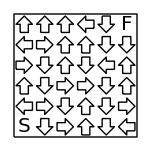

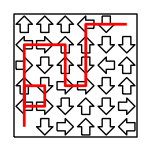

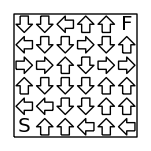

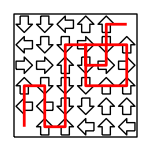

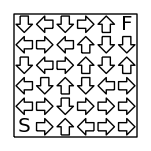

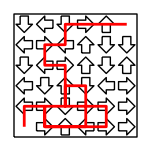

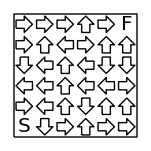

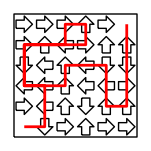

-Graphics-

-Graphics-

-Graphics-

«121 more identical outputs»

27

-Graphics-

-Graphics-

21

-Graphics-

-Graphics-

15

-Graphics-

-Graphics-

15

-Graphics-

-Graphics-

15

-Graphics-

-Graphics-

13

-Graphics-

-Graphics-

19

-Graphics-

-Graphics-

19

-Graphics-

-Graphics-

13

-Graphics-

-Graphics-

15

-Graphics-

-Graphics-

19

-Graphics-

-Graphics-

13

-Graphics-

-Graphics-

13

-Graphics-

-Graphics-

19

-Graphics-

-Graphics-

31

-Graphics-

-Graphics-

13

-Graphics-

-Graphics-